# Lab 4 - Series Expansions

```mathematica
Needs["PlotLegends`"]
dir = NotebookDirectory[];
SetDirectory[dir];
```

Series Sin and Cosine around x=0 out to n terms.

```mathematica
SerCos[x_,n_] := Normal[Series[Cos[a], {a,0,n}]] /. a->x
```

```mathematica
SerSin[x_,n_] := Normal[Series[Sin[a], {a,0,n}]] /. a->x
```

Evaluate the difference between SerSin and Sin.

```mathematica
serSinDiff[x_, n_] := SerSin[x,n] - Sin[x]
```

```mathematica
data = Table[serSinDiff[x,n], {n, 5,11,2}]
```

{x-x^3/6+x^5/120-Sin[x],x-x^3/6+x^5/120-x^7/5040-Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800-Sin[x]}

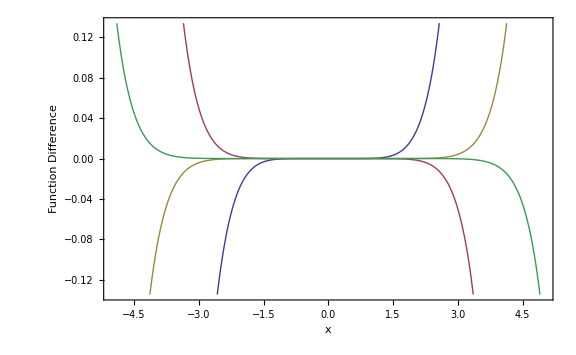

```mathematica
graph = Plot[{data[[1]],data[[2]],data[[3]],data[[4]]},{x,-5,5}, Frame -> True, FrameLabel->{{"Function Difference", ""},{"x", "SerSin[x,n] - Sin[x]"}},PlotLegend->{Style["n=5",20],Style["n=7",20],Style["n=9",20],Style["n=11",20]},LegendPosition->{.85,-0.4}, PlotStyle-> Thick, ImageSize-> Large, LabelStyle -> Larger]
```

```mathematica
Export["difference.png", graph]
```

difference.png

Define SerCos^2 + SerSin^2

```mathematica
sumSquareSer[x_,n_] := SerCos[x,n]^2 + SerSin[x,n]^2
```

```mathematica
data = Table[sumSquareSer[x,n], {n, 5,11,2}]
```

{(1-x^2/2+x^4/24)^2+(x-x^3/6+x^5/120)^2,(1-x^2/2+x^4/24-x^6/720)^2+(x-x^3/6+x^5/120-x^7/5040)^2,(1-x^2/2+x^4/24-x^6/720+x^8/40320)^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2,(1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800)^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800)^2}

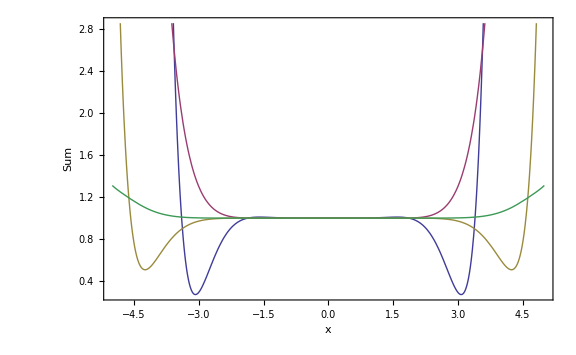

```mathematica
graph = Plot[{data[[1]],data[[2]],data[[3]],data[[4]]},{x,-5,5}, Frame -> True, FrameLabel->{{"Sum", ""},{"x", "SerSin[x,n]^2 + SerCos[x,n]^2"}},PlotLegend->{Style["n=5",20],Style["n=7",20],Style["n=9",20],Style["n=11",20]},LegendPosition->{.85,-0.4}, PlotStyle-> Thick, ImageSize-> Large, LabelStyle -> Larger]
```

```mathematica
Export["sumSer.png",graph]
```

sumSer.png

Define SerCosSq and SerSinSq.

```mathematica
SerCosSq[x_,n_] := Normal[Series[Cos[a]^2, {a,0,n}]] /. a->x
```

```mathematica
SerSinSq[x_,n_] := Normal[Series[Sin[a]^2, {a,0,n}]] /. a->x
```

```mathematica
sumSerSquare[x_,n_] := SerCosSq[x,n] + SerSinSq[x,n]
```

```mathematica
data = Table[sumSerSquare[x,n], {n, 5,100,1}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

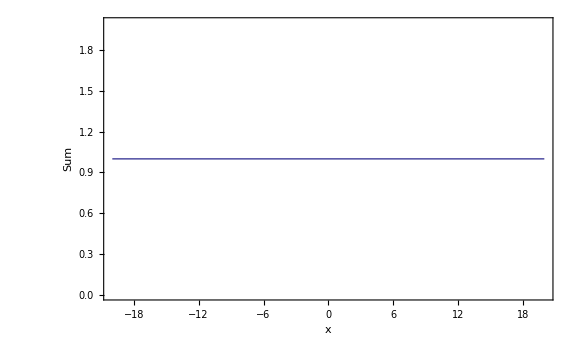

```mathematica
graph = Plot[data[[Length[data]]],{x,-20,20}, Frame -> True, FrameLabel->{{"Sum", ""},{"x", "SerSinSq[x,n] + SerCosSq[x,n]"}},PlotStyle-> Thick,PlotLegend->{Style["n=100",20]},LegendPosition->{.85,-0.4}, ImageSize-> Large,LabelStyle -> Larger]
```

```mathematica
Export["sumSerSq.png",graph]
```

sumSerSq.png

Define three rotation matrices

```mathematica
rX[th_] := {{1,0,0},{0,Cos[th], Sin[th]},{0, -Sin[th], Cos[th]}}
```

```mathematica
MatrixForm[rX[x]]
```

(1 | 0 | 0
0 | Cos[x] | Sin[x]
0 | -Sin[x] | Cos[x])

```mathematica
rY[ski_] := {{Cos[ski],0,Sin[ski]},{0,1, 0},{-Sin[ski],0, Cos[ski]}}
```

```mathematica
MatrixForm[rY[x]]
```

(Cos[x] | 0 | Sin[x]
0 | 1 | 0
-Sin[x] | 0 | Cos[x])

```mathematica
rZ[phi_] := {{Cos[phi],Sin[phi],0},{-Sin[phi],Cos[phi], 0},{0, -0, 1}}
```

```mathematica
MatrixForm[rZ[x]]
```

(Cos[x] | Sin[x] | 0
-Sin[x] | Cos[x] | 0
0 | 0 | 1)

Full Rotation

```mathematica
Rot3[a1_,a2_,a3_] := rZ[a1].rX[a2].rZ[a3]
```

```mathematica
MatrixForm[Rot3[x,y,z]]
```

(Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z] | Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z] | Sin[x] Sin[y]
-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z] | Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z] | Cos[x] Sin[y]
Sin[y] Sin[z] | -Cos[z] Sin[y] | Cos[y])

```mathematica
MatrixForm[Simplify[Rot3[x,y,z]]]
```

(Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z] | Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z] | Sin[x] Sin[y]
-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z] | Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z] | Cos[x] Sin[y]
Sin[y] Sin[z] | -Cos[z] Sin[y] | Cos[y])

Rotational inverse with negative angles

```mathematica
Rot3Inverse[a1_,a2_,a3_] := Rot3[-a3, -a2, -a1]
```

ReverseAngles times Regular is the identity.

```mathematica
revAngle = MatrixForm[Rot3Inverse[x,y,z].Rot3[x,y,z]]
```

(Sin[y]^2 Sin[z]^2+(-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z])^2+(Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z])^2 | -Cos[z] Sin[y]^2 Sin[z]+(-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z]) (Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z])+(Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z]) (Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z]) | Cos[y] Sin[y] Sin[z]+Cos[x] Sin[y] (-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z])+Sin[x] Sin[y] (Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z])
-Cos[z] Sin[y]^2 Sin[z]+(-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z]) (Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z])+(Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z]) (Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z]) | Cos[z]^2 Sin[y]^2+(Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z])^2+(Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z])^2 | -Cos[y] Cos[z] Sin[y]+Sin[x] Sin[y] (Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z])+Cos[x] Sin[y] (Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z])
Cos[y] Sin[y] Sin[z]+Cos[x] Sin[y] (-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z])+Sin[x] Sin[y] (Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z]) | -Cos[y] Cos[z] Sin[y]+Sin[x] Sin[y] (Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z])+Cos[x] Sin[y] (Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z]) | Cos[y]^2+Cos[x]^2 Sin[y]^2+Sin[x]^2 Sin[y]^2)

```mathematica
Simplify[revAngle]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Inverse Matrix times Matrix is the Identity

```mathematica
invFunc = MatrixForm[Inverse[Rot3[x,y,z]].Rot3[x,y,z]]
```

(((-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z]) (-Cos[y]^2 Cos[z] Sin[x]-Cos[z] Sin[x] Sin[y]^2-Cos[x] Cos[y] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z]) (Cos[x] Cos[y]^2 Cos[z]+Cos[x] Cos[z] Sin[y]^2-Cos[y] Sin[x] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Sin[y] Sin[z] (Cos[x]^2 Sin[y] Sin[z]+Sin[x]^2 Sin[y] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | ((-Cos[y]^2 Cos[z] Sin[x]-Cos[z] Sin[x] Sin[y]^2-Cos[x] Cos[y] Sin[z]) (Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z]) (Cos[x] Cos[y]^2 Cos[z]+Cos[x] Cos[z] Sin[y]^2-Cos[y] Sin[x] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)-(Cos[z] Sin[y] (Cos[x]^2 Sin[y] Sin[z]+Sin[x]^2 Sin[y] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | (Cos[x] Sin[y] (-Cos[y]^2 Cos[z] Sin[x]-Cos[z] Sin[x] Sin[y]^2-Cos[x] Cos[y] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Sin[x] Sin[y] (Cos[x] Cos[y]^2 Cos[z]+Cos[x] Cos[z] Sin[y]^2-Cos[y] Sin[x] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Cos[y] (Cos[x]^2 Sin[y] Sin[z]+Sin[x]^2 Sin[y] Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)
(Sin[y] (-Cos[x]^2 Cos[z] Sin[y]-Cos[z] Sin[x]^2 Sin[y]) Sin[z])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z]) (Cos[y] Cos[z] Sin[x]+Cos[x] Cos[y]^2 Sin[z]+Cos[x] Sin[y]^2 Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z]) (Cos[x] Cos[y] Cos[z]-Cos[y]^2 Sin[x] Sin[z]-Sin[x] Sin[y]^2 Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | -(Cos[z] Sin[y] (-Cos[x]^2 Cos[z] Sin[y]-Cos[z] Sin[x]^2 Sin[y]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z]) (Cos[y] Cos[z] Sin[x]+Cos[x] Cos[y]^2 Sin[z]+Cos[x] Sin[y]^2 Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z]) (Cos[x] Cos[y] Cos[z]-Cos[y]^2 Sin[x] Sin[z]-Sin[x] Sin[y]^2 Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | (Cos[y] (-Cos[x]^2 Cos[z] Sin[y]-Cos[z] Sin[x]^2 Sin[y]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Sin[x] Sin[y] (Cos[y] Cos[z] Sin[x]+Cos[x] Cos[y]^2 Sin[z]+Cos[x] Sin[y]^2 Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Cos[x] Sin[y] (Cos[x] Cos[y] Cos[z]-Cos[y]^2 Sin[x] Sin[z]-Sin[x] Sin[y]^2 Sin[z]))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)
(Sin[y] Sin[z] (Cos[x]^2 Cos[y] Cos[z]^2+Cos[y] Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[y] Sin[z]^2+Cos[y] Sin[x]^2 Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((-Cos[z] Sin[x]-Cos[x] Cos[y] Sin[z]) (Cos[x] Cos[z]^2 Sin[y]+Cos[x] Sin[y] Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[x] Cos[z]-Cos[y] Sin[x] Sin[z]) (Cos[z]^2 Sin[x] Sin[y]+Sin[x] Sin[y] Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | -(Cos[z] Sin[y] (Cos[x]^2 Cos[y] Cos[z]^2+Cos[y] Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[y] Sin[z]^2+Cos[y] Sin[x]^2 Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[x] Cos[y] Cos[z]-Sin[x] Sin[z]) (Cos[x] Cos[z]^2 Sin[y]+Cos[x] Sin[y] Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+((Cos[y] Cos[z] Sin[x]+Cos[x] Sin[z]) (Cos[z]^2 Sin[x] Sin[y]+Sin[x] Sin[y] Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | (Cos[y] (Cos[x]^2 Cos[y] Cos[z]^2+Cos[y] Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[y] Sin[z]^2+Cos[y] Sin[x]^2 Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Cos[x] Sin[y] (Cos[x] Cos[z]^2 Sin[y]+Cos[x] Sin[y] Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)+(Sin[x] Sin[y] (Cos[z]^2 Sin[x] Sin[y]+Sin[x] Sin[y] Sin[z]^2))/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2))

```mathematica
Simplify[invFunc]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
invDiff[x_,y_,z_] := Inverse[Rot3[x,y,z]] - Rot3Inverse[x,y,z]
```

```mathematica
diff = MatrixForm[invDiff[x,y,z]]
```

(-Cos[x] Cos[z]+Cos[y] Sin[x] Sin[z]+(Cos[x] Cos[y]^2 Cos[z]+Cos[x] Cos[z] Sin[y]^2-Cos[y] Sin[x] Sin[z])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | Cos[z] Sin[x]+Cos[x] Cos[y] Sin[z]+(-Cos[y]^2 Cos[z] Sin[x]-Cos[z] Sin[x] Sin[y]^2-Cos[x] Cos[y] Sin[z])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | -Sin[y] Sin[z]+(Cos[x]^2 Sin[y] Sin[z]+Sin[x]^2 Sin[y] Sin[z])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)
-Cos[y] Cos[z] Sin[x]-Cos[x] Sin[z]+(Cos[y] Cos[z] Sin[x]+Cos[x] Cos[y]^2 Sin[z]+Cos[x] Sin[y]^2 Sin[z])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | -Cos[x] Cos[y] Cos[z]+Sin[x] Sin[z]+(Cos[x] Cos[y] Cos[z]-Cos[y]^2 Sin[x] Sin[z]-Sin[x] Sin[y]^2 Sin[z])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | Cos[z] Sin[y]+(-Cos[x]^2 Cos[z] Sin[y]-Cos[z] Sin[x]^2 Sin[y])/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2)
-Sin[x] Sin[y]+(Cos[z]^2 Sin[x] Sin[y]+Sin[x] Sin[y] Sin[z]^2)/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | -Cos[x] Sin[y]+(Cos[x] Cos[z]^2 Sin[y]+Cos[x] Sin[y] Sin[z]^2)/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2) | -Cos[y]+(Cos[x]^2 Cos[y] Cos[z]^2+Cos[y] Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[y] Sin[z]^2+Cos[y] Sin[x]^2 Sin[z]^2)/(Cos[x]^2 Cos[y]^2 Cos[z]^2+Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2+Cos[x]^2 Cos[y]^2 Sin[z]^2+Cos[y]^2 Sin[x]^2 Sin[z]^2+Cos[x]^2 Sin[y]^2 Sin[z]^2+Sin[x]^2 Sin[y]^2 Sin[z]^2))

```mathematica
Simplify[diff]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
Export["series.pdf", EvaluationNotebook[]]
```

series.pdf